```mathematica
Clear["Global`*"];
RandomSeed[0];
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<"Sampler1`";
```

```mathematica
σ=0.00001;
```

```mathematica
SIGMA={{σ^2,0},{0,1}};
```

```mathematica
U[x_,y_]=1/2 Simplify[{x,y}.LinearSolve[SIGMA,{x,y}]];
```

```mathematica
dU[x_,y_]=GradientG[U[x,y],{x,y}];
```

```mathematica
ddU[x_,y_]=HessianH[U[x,y],{x,y}];
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{1.×10^10,0.},{0.,1.}} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

1001 263.637 10.9862 0.103298 0.315131 27.2974 290.935 455.577 9.90099×10^-6 0.00105294 True {1,10,11} {2,3,9}

2002 580.551 3.80499 0.858047 0.250063 8.36683 278.02 588.918 9.90099×10^-6 0.00571527 False {1,2,3,10,11} {1,11}

3003 260.271 15.1551 0.100029 0.287974 7.47517 267.746 600.6 9.90099×10^-6 0.00868029 True {1,10} {2,6,9}

4004 598.712 4.68259 0.631399 0.408746 4.84292 262.104 603.555 9.80296×10^-6 0.0108045 False {1,2,8,10} {1,11}

5005 254.049 17.2208 0.300614 0.397889 4.81029 258.859 603.555 9.6098×10^-6 0.0124195 True {1,11} {3,6,9}

6006 594.152 4.01878 0.678859 0.334565 9.40296 258.859 603.555 9.6098×10^-6 0.0124195 False {1,3,4,6,11} {1,11}

7007 251.823 6.53636 0.428715 0.484211 7.03601 258.859 603.555 9.6098×10^-6 0.0124195 True {1,2,3,4,7,10,11} {2,3,6,7,9,11}

8008 596.84 2.60525 0.540272 0.397897 6.71436 258.859 603.555 9.6098×10^-6 0.0124195 False {1,4,5,11} {1,11}

9009 250.681 8.27229 0.219387 0.306859 8.17841 258.859 603.555 9.6098×10^-6 0.0124195 True {1,4,7,11} {2,3,9}

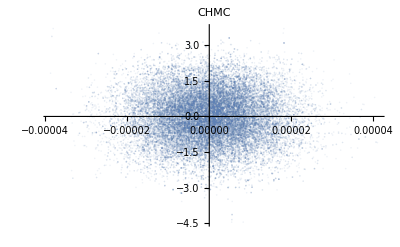

```mathematica
QS=hmc[U,dU,ddU,2,5000,10000,True,True];
ListPlot[QS,PlotLabel->CHMC,PlotStyle->Opacity[.1]]
```

1001 -220.336 10.7552 0.320695 0.471433 520.336 300 300 0.00001 0.00001 True {1,3,9,10,11} {1,2,3,9,10,11}

2002 -224.426 9.25099 0.145647 0.282514 524.426 300 300 0.00001 0.00001 True {1,10} {2,3,9}

3003 -222.011 6.76312 0.534081 0.48953 522.011 300 300 9.90099×10^-6 0.00001 True {1,10,11} {2,3,6,9}

4004 -218.865 5.94363 0.445244 0.414718 518.865 300 300 9.90099×10^-6 0.00001 True {1,3,4,7,9,10} {1,2,9,11}

5005 -222.797 15.5537 0.457034 0.486869 522.797 300 300 9.90099×10^-6 0.00001 True {1,2,7,9,10,11} {1,2,3,4,9,10}

6006 -225.987 7.80723 0.256719 0.346795 525.987 300 300 9.90099×10^-6 0.00001 True {1,4,9,10} {1,2,9}

7007 -222.943 11.3985 0.421198 0.500386 522.943 300 300 9.90099×10^-6 0.00001 True {1,2,10,11} {2,3,6,9,10}

8008 -223.25 6.04552 0.410655 0.465075 523.25 300 300 9.90099×10^-6 0.00001 True {1,10,11} {2,3,9}

9009 -221.992 8.84601 0.426708 0.416854 521.992 300 300 9.90099×10^-6 0.00001 True {1,3,4,10,11} {2,3,5,9,11}

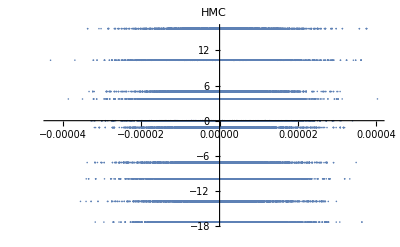

```mathematica
QS=hmc[U,dU,ddU,2,5000,10000,True,False];
ListPlot[QS,PlotLabel->HMC]
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{1.×10^10,0.},{0.,1.}} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

1001 -4.91307×10^10 7.20035 0.5 0.527046 4.91307×10^10 300 300 0.00001 0.0000120811 False {1,2,6,11} {1,5,11}

2002 -4.91299×10^10 5.88709 0.504336 0.522565 4.91299×10^10 300 300 0.00001 0.0000164463 False {1,6,11} {1,2,11}

3003 -4.91282×10^10 7.73542 0.6 0.516398 4.91282×10^10 300 300 0.00001 0.0000240038 False {1,11} {1,4,5,6,11}

4004 -4.91248×10^10 1.40021 0.4 0.516398 4.91248×10^10 300 300 0.00001 0.0000330039 False {1,2,3,11} {1,11}

5005 -4.91166×10^10 4.47245 0.6 0.516398 4.91166×10^10 300 300 0.00001 0.0000593644 False {1,2,3,10,11} {1,4,11}

6006 -4.91022×10^10 4.89658 0.500241 0.526793 4.91022×10^10 300 300 0.00001 0.0000593644 False {1,11} {1,11}

7007 -4.90879×10^10 3.17002 0.4 0.516398 4.90879×10^10 300 300 0.00001 0.0000593644 False {1,3,11} {1,3,7,11}

8008 -4.90734×10^10 3.11101 0.5 0.527046 4.90734×10^10 300 300 0.00001 0.0000593644 False {1,2,11} {1,3,11}

9009 -4.9059×10^10 6.46063 0.5 0.527046 4.9059×10^10 300 300 0.00001 0.0000593644 False {1,2,3,11} {1,11}

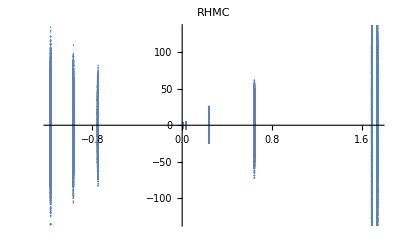

```mathematica
QS=hmc[U,dU,ddU,2,5000,10000,False,False];
ListPlot[QS,PlotLabel->RHMC]
```